# Rossler

The previous notebook implemented return maps, their section derivatives, and a Newton solve on the vertical section  Σ^-={y_1=c,-y_2-y_3<0}⊂ℝ^3 for Rossler.  This notebook uses these tools to explore the behavior of orbits for  a range of values of c.   The code cell below contains many of the functions we have built so far.

### Code

```mathematica
Clear[f,dyf,ReturnMapAndTimeAndJ]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x + a y,b + z(x-c)}
dyf[{a_,b_,c_}][{x_,y_,z_}]:=({{0, -1, -1}, {1, a, 0}, {z, 0, x-c}}) 
dcf[{a_,b_,c_}][{x_,y_,z_}]:={0,0,-z}
ReturnMapAndTimeAndJ[{a_,b_,c_},{f_,dyf_}][{u1_,u2_}]:= Module[{y0,TMin=0.001,TMax=123,
tVal,yVal,JVal,ySol,JSol,y,J,t},
y0={c,u1,u2};
{tVal,yVal,JVal} = Reap[
{ySol,JSol}= NDSolveValue[ {
y'[t]==f[{a,b,c}][y[t]],
J'[t]==dyf[{a,b,c}][y[t]].J[t],
y[0]==y0,J[0]==IdentityMatrix[3],
WhenEvent[Indexed[y[t],1]-c <0,If[t>TMin, Sow[{t,y[t],J[t]}]; "StopIntegration"]]
(* I have no idea why I had to use indexed instead of [[]] in here! *)
},{y,J},{t,0,TMax}];
]⟦2,1,1⟧
]
```

```mathematica
pAndDp[{a_,b_,c_},{f_,dcf_}][{u1_,u2_}]:= Module[{t,p,J,Dp,f1,f2,f3},
{t,p,J}=ReturnMapAndTimeAndJ[{a,b,c},{f,dyf}][{u1,u2}];
{f1,f2,f3}=f[{a,b,c}][p];
Dp=({{J⟦2,2⟧, J⟦2,3⟧}, {J⟦3,2⟧, J⟦3,3⟧}})-1/f1({{f2 J⟦1,2⟧, f2 J⟦1,3⟧}, {f3 J⟦1,2⟧, f3 J⟦1,3⟧}});
{p⟦2;;3⟧,Dp}
]
```

Here are our two solvers.

```mathematica
FPNewt[{a_,b_,c_},{f_,dyf_},Tol_][u0_]:= Module[{u=u0,p,Dp,err,n=0,nMax=10},
While[
{p,Dp}=pAndDp[{a,b,c},{f,dyf}][u];
err=Norm[p-u];And[err>Tol,n<nMax],
n++;u=u-LinearSolve[Dp-IdentityMatrix[2],p-u]
(* Print[{n,u, err}]*)]; 
{n,u,err}
]

FPNonNewt[{a_,b_,c_},{f_,dyf_},Tol_][u0_]:= Module[{u=u0,p,Dp,err,n=0,nMax=10},
While[
{p,Dp}=pAndDp[{a,b,c},{f,dyf}][u];
err=Norm[p-u];And[err>Tol,n<nMax],
n++;u=p
(* Print[{n,u, err}] *)
];
{n,u,err}
]
```

Remember the Newton one is much faster and the Non-Newton solver can not work for unstable fixed points.  I am going to comment out the print statements.

```mathematica
{a,b,c}={0.2,0.2,2.6};
u0={2.3,3.4};
Tol=10^-12;
FPNewt[{a,b,c},{f,dyf},Tol][u0]
```

{3,{2.30454,3.3231},8.72497×10^-15}

```mathematica
{a,b,c}={0.2,0.2,2.6};
u0={2.3,3.4};
Tol=10^-12;
FPNonNewt[{a,b,c},{f,dyf},Tol][u0]
```

{10,{2.30346,3.33397},0.0200961}

One more piece of code to collect section points from a start point and throw away the first batch.

```mathematica
CollectSectionPoints[{a_,b_,c_},{f_}][u0_]:= Module[
{y0 = Join[{c},u0],y,t,TMin=10^3,TMax=10^4},
Reap[NDSolveValue[{y'[t]==f[{a,b,c}][y[t]],y[0]==y0, 
WhenEvent[Indexed[y[t],1]-c<0,If[t>TMin, Sow[y[t]]]] },
y,{t,0, TMax}]]⟦2,1⟧
]
```

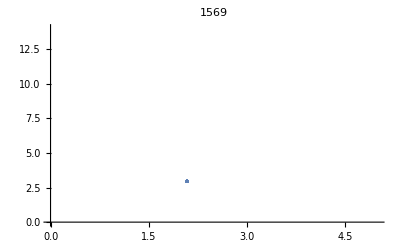

```mathematica
{a,b,c}={0.2,0.2,2.3};
u0={2.3,3.4};
PtData=CollectSectionPoints[{a,b,c},{f}][u0];
ListPlot[PtData⟦All,2;;3⟧,PlotRange->{{0,5},{0,14}},PlotLabel->Length[PtData]]
```

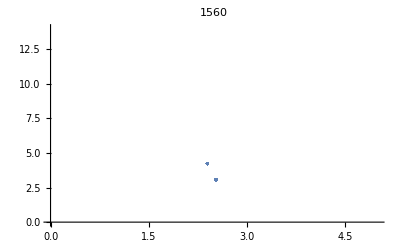

```mathematica
{a,b,c}={0.2,0.2,2.85};
u0={2.3,3.4};
PtData=CollectSectionPoints[{a,b,c},{f}][u0];
ListPlot[PtData⟦All,2;;3⟧,PlotRange->{{0,5},{0,14}},PlotLabel->Length[PtData]]
```

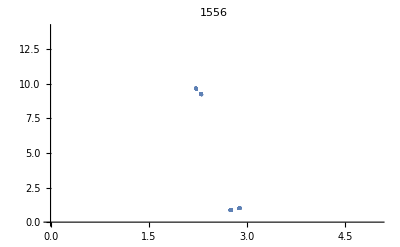

```mathematica
{a,b,c}={0.2,0.2,3.84};
u0={2.3,3.4};
PtData=CollectSectionPoints[{a,b,c},{f}][u0];
ListPlot[PtData⟦All,2;;3⟧,PlotRange->{{0,5},{0,14}},PlotLabel->Length[PtData]]
```

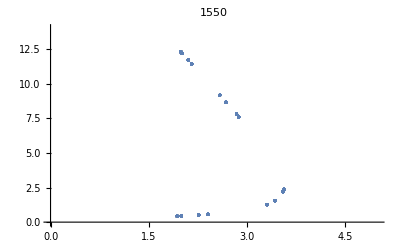

```mathematica
{a,b,c}={0.2,0.2,4.2};
u0={2.3,3.4};
PtData=CollectSectionPoints[{a,b,c},{f}][u0];
ListPlot[PtData⟦All,2;;3⟧,PlotRange->{{0,5},{0,14}},PlotLabel->Length[PtData]]
```

### Bifurcations in c

From https://en.wikipedia.org/wiki/Bifurcation_theory

Bifurcation theory is the mathematical study of changes in the qualitative or topological structure of a given family of curves, such as the integral curves of a family of vector fields, and the solutions of a family of differential equations. Most commonly applied to the mathematical study of dynamical systems, a bifurcation occurs when a small smooth change made to the parameter values (the bifurcation parameters) of a system causes a sudden “qualitative” or topological change in its behavior.

The Rossler bifurcates as c changes. The picture below shows the system going from attractive single loop solutions to attractive double loop solutions, to attractive four loop solutions.

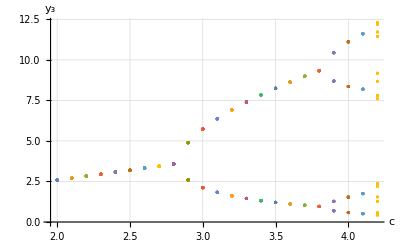

```mathematica
{a,b}={0.2,0.2};
u0={2.3,3.4};
BifurcationData=Table[
PtData=CollectSectionPoints[{a,b,c},{f}][u0];
{ConstantArray[c,40],PtData⟦-40;;-1,3⟧}ᵀ,
{c, 2,4.2,0.1}];
Pic=ListPlot[BifurcationData,GridLines->Automatic,AxesLabel->{"c","y_3"}]
```

Newton’s method will fill this in more without waiting forever!  The plot shows a single loop solution with c=2.0 and y_3≈2.6.  We could work out a better guess for y_2 but we will just use y_2=2 and run Newton’s method

```mathematica
{a,b,c}={0.2,0.2,2.0};
dc=0.01;
u0={2,2.6}; Tol=10^-12;
{n,u, err}=FPNewt[{a,b,c},{f,dyf},Tol][u0]
```

{4,{1.84432,2.58013},1.16229×10^-14}

So we know an accurate value for c=2. This will give a reasonable guess for the value for c=2.05

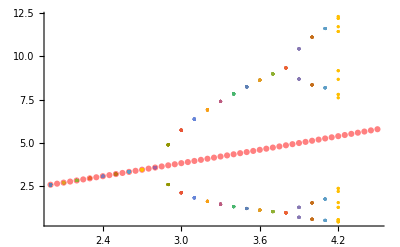

```mathematica
{a,b,c}={0.2,0.2,2.0};
dc=0.01;
u0={1.8443237265215302,2.580129423035227}; Tol=10^-12; u=u0;
SingleLoopData=Table[{n,u, err}=FPNewt[{a,b,c},{f,dyf},Tol][u];
{c,u⟦2⟧},
{c,2.0, 4.5,0.05}];
Show[ListPlot[SingleLoopData,PlotStyle->Pink],Pic,
PlotRange->All ]
```

I guess we want to solve the twice around system 
	q_2 | = | p(q_1)
q_1 | = | p(q_2)⟹ | p(q_1)-q_2 | = | 0
p(q_2)-q_1 | = | 0⟹f(q)=0
where 
	q=(q_1
q_2) and f(q)=(p(q_1)-q_2
p(q_2)-q_1) and Df(q)=(Dp(q_1) | -I_2
-I_2 | Dp(q_2))  
Newton’s method (where q^k indicates the kth iteration of the stack) is
	q^(k+1)=q^k-(Df(q^k))^-1(f(q^k)-q^k)
This is easy enough to implement.  I am going to try to compute the c=3.5 twice around blue orbit.   A rough estimate of a starting point is {2.0,8.0} for the high section point and {3.0,1.0} for the low section point.

```mathematica
{a,b,c}={0.2,0.2,3.5};
u={2.2,8.2,2.8,1.2}
(* 1 *)
{p1,Df1}=pAndDp[{a,b,c},{f,dyf}][u⟦{1,2}⟧];
{p2,Df2}=pAndDp[{a,b,c},{f,dyf}][u⟦{3,4}⟧];
A=ArrayFlatten[({{Df1, -IdentityMatrix[2]}, {-IdentityMatrix[2], Df2}})];
u=u-LinearSolve[A,Flatten[{p1-u⟦{3,4}⟧,p2-u⟦{1,2}⟧}]]
(* 2 *)
{p1,Df1}=pAndDp[{a,b,c},{f,dyf}][u⟦{1,2}⟧];
{p2,Df2}=pAndDp[{a,b,c},{f,dyf}][u⟦{3,4}⟧];
A=ArrayFlatten[({{Df1, -IdentityMatrix[2]}, {-IdentityMatrix[2], Df2}})];
u=u-LinearSolve[A,Flatten[{p1-u⟦{3,4}⟧,p2-u⟦{1,2}⟧}]]
(* 3 *)
{p1,Df1}=pAndDp[{a,b,c},{f,dyf}][u⟦{1,2}⟧];
{p2,Df2}=pAndDp[{a,b,c},{f,dyf}][u⟦{3,4}⟧];
A=ArrayFlatten[({{Df1, -IdentityMatrix[2]}, {-IdentityMatrix[2], Df2}})];
u=u-LinearSolve[A,Flatten[{p1-u⟦{3,4}⟧,p2-u⟦{1,2}⟧}]]
```

{2.2,8.2,2.8,1.2}

{2.23286,8.24839,2.80757,1.20317}

{2.23384,8.24305,2.80787,1.20652}

{2.23384,8.24305,2.80787,1.20652}

```mathematica
u=u-LinearSolve[A, Join[p1-q2-q1,p2-q1-q2]],
{2}]//TableForm
```

{2.2,8.2,2.8,1.2}

2.56734 | 3.66882 | 0.802391 | -1.17147
-1.16568 | -6.4871 | 3.31285 | -3.55251

```mathematica
MatrixForm[A]
```

(1.06109 | -0.0452538 | -1 | 0
1.68777 | -0.0719811 | 0 | -1
-1 | 0 | -1.0295 | 0.390565
0 | -1 | 5.57008 | -2.11314)

```mathematica
CollectSectionPoints[{a,b,c},{f}][{2.0,8.0}]⟦-4;;-1⟧
```

{{3.5,2.80787,1.20652},{3.5,2.23384,8.24305},{3.5,2.80787,1.20652},{3.5,2.23384,8.24305}}

2.564 | 7.73883 | 2.982 | 1.99875
4.25371 | 0.0581268 | 3.65833 | 8.94417
3.35611 | 6.6031 | 4.69545 | 4.85242

```mathematica
A=ArrayFlatten[({{Df1, -IdentityMatrix[2]}, {-IdentityMatrix[2], Df2}})];
u=u-LinearSolve[A, Flatten[{p1-q2,p2-q1}]]
```

{2.928,7.27767,3.16401,2.79749}

```mathematica
NewtFP[{a,b,c},{f,df
```